```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u→{u,…},c_v→{v,…},…] links the controls to the specified controllers on an external device.

```mathematica
Manipulate[ParametricPlot[{Sin[2x]+a x,Sin[5x+t]+b x},{x,0,6Pi}],{t,0,2Pi},{a,0,1},{b,0,1}]
```

```mathematica
Animate[ParametricPlot[{2Sin[2x]+x,2Sin[5x+t]+x},{x,0,6Pi}],{t,0,2Pi}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adam/Dropbox/personal/projects/mathca

```mathematica
Export["./choker.gif",Table[ParametricPlot[{2Sin[2x]+x,2Sin[5x+t]+x},{x,0,6Pi}],{t,0,2Pi-.001,Pi/10}]]
```

/home/adam/choker.gif

```mathematica
Export["./choker2.gif",Table[ParametricPlot[{2Sin[2x]+x,2Cos[r x]+x},{x,0,6Pi},PlotRange->{{0,20},{0,20}}],{r,0,5,.1}]]
```

./choker2.gif

```mathematica
Animate[ParametricPlot[{2Sin[2x]+x,2Cos[r x]+x},{x,0,6Pi},PlotRange->{{0,20},{0,20}}],{r,0,5}]
```

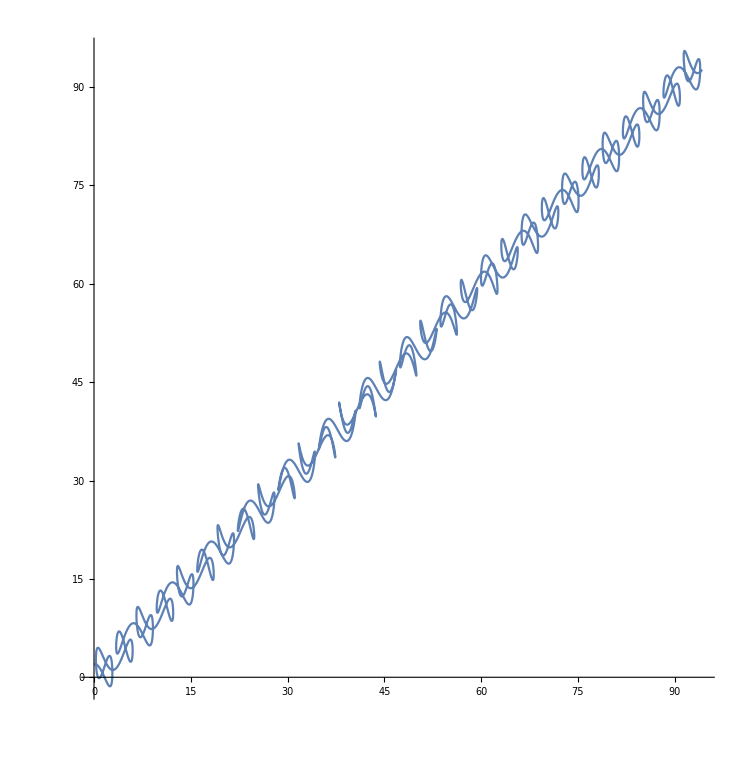

```mathematica
ParametricPlot[{2Sin[2x]+x,2Cos[5.04 x]+x},{x,0,30Pi}]
```